# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 5

4. - Calcular el dominio de la función Log[√(x+1)] Junio 21

```mathematica
Log[√(x+1)]
```

```mathematica
f[X_]:=Sin[X]
```

```mathematica
{f[0],f[1],f[2]}
```

{0,Sin[1],Sin[2]}

```mathematica
N[{f[0],f[1],f[2]}]
```

{0.,0.841471,0.909297}

Funciones a trozos:

```mathematica
g[X_]:=Which[X≤3, x-2,3<X<6,2X+1,6≤x,X^2/(3X+1)]
```

```mathematica
Clear[f]
```

```mathematica
Plot[f[X],[X,-10,10]]
```

Limites y asíntotas:

```mathematica
Limit[ (x^2-4)/(x-2) ,x->2]
```

4

```mathematica
Limit[(x^2+3)/(x^2+1), x-> Infinity]
```

1

Limites laterales

```mathematica
Limit[g[x],x->3,Direction->1]
```

1

```mathematica
Limit[g[x],x->3,Direction->-1]
```

7

Limites que no existen

```mathematica
Limit[Cos[1/x],x->0]
```

Indeterminate

```mathematica
Information[Indeterminate]
```

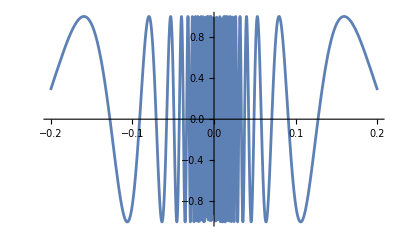

```mathematica
Plot[Cos[1/x],{x,-0.2,0.2}]
```

Limites e^x/(1+e^x) en + - infinito

```mathematica
Limit[ⅇ^x/(1+ⅇ^x),x->Infinity]
```

1

Modificaciones a la gráfica de una función

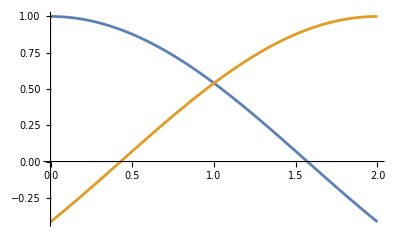

```mathematica
Plot[{Cos[x],Cos[2-x]},{x,0,2}]
```

Para representar la temperatura minima, 11, y la máxima, 23, en Jaén.

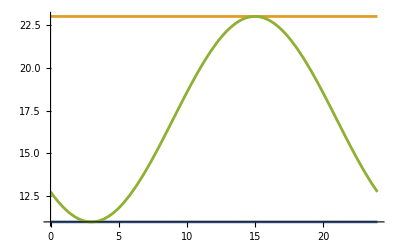

```mathematica
Plot[{11,23,((11+23)/2)+6*Cos[((x-15)*2Pi/24)]},{x,0,24}]
```

Para representar las horas de sol durante todo el año en Jaén.

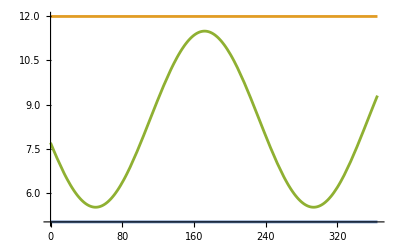

```mathematica
Plot[{5,12,(5+12)/2+3Cos[3Pi*(x-31-28-31-30-31-21)/365]},{x,0,365}]
```

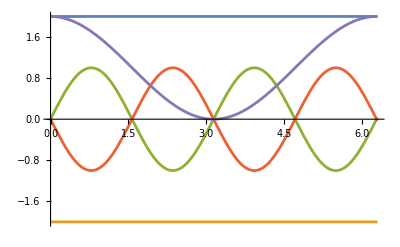

```mathematica
Plot[{2,-2,Sin[2x],-Sin[2x],1+Cos[x]},{x,0,6.3}]
```